```mathematica
Exit[]
```

# Optimization with Equality Constraints

## Example 1

Maximize utility subject to budget constraint (assuming px=3 and py=1)

```mathematica
u[x_,y_]:=x*y
```

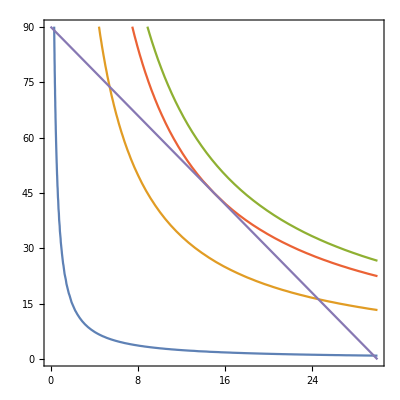

```mathematica
ContourPlot[{u[x,y]==30,u[x,y]==400,u[x,y]==800,u[x,y]==675,3*x+1*y==90},{x,0,30},{y,0,90}]
```

### Gradient vectors

```mathematica
Mu=Grad[u[x,y],{x,y}]
```

{y,x}

```mathematica
p=Grad[3*x+1*y,{x,y}]
```

{3,1}

#### The gradient of a function is perpendicular to the curve level of the function

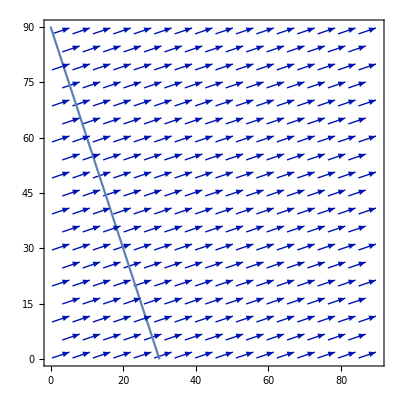

```mathematica
p1 := VectorPlot[p, {x, 0, 90}, {y, 0, 90}]
p2 := ContourPlot[3*x + y == 90, {x, 0, 90}, {y, 0, 90}]
Show[p1, p2]
```

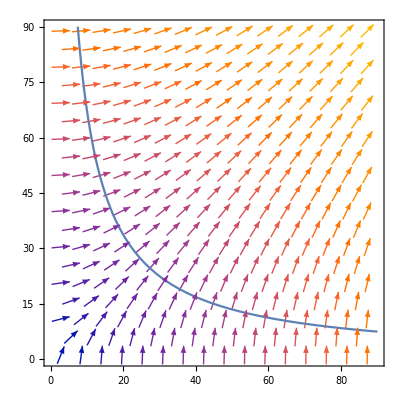

```mathematica
p3:=VectorPlot[Mu,{x,0,90},{y,0,90}]
p4:=ContourPlot[u[x,y]==675,{x,0,90},{y,0,90}]
Show[p3,p4]
```

#### If two curves are tangent at a point then the corresponding gradients at the point must be proportional (one is a multiple of the other)

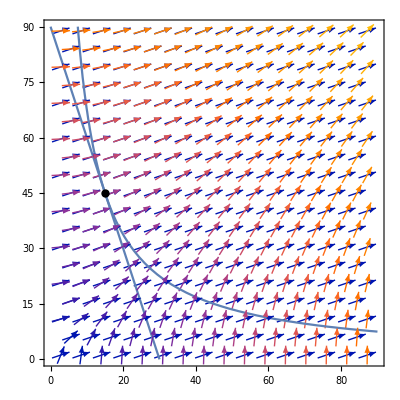

```mathematica
p5:=Graphics[{PointSize[.015],Point[{15,45}]}]
Show[p1,p2,p3,p4,p5]
```

#### Solving for a point in the budget line at which the gradients (of the utility and of the budget) are proportional:

```mathematica
Solve[{y==λ 3 ,x==λ ,3*x+1*y==90},{x,y,λ}]
```

{{x→15,y→45,λ→15}}

```mathematica
Mu/.{x->15,y->45,λ->15}
p
```

{45,15}

{3,1}

## Example 2

```mathematica
D[f[x]]
```

f[x]

```mathematica
(2*x)′
```

2 x ′

Minimize cost of production subject to quantity constraint  (assuming w=2 and r=8)

```mathematica
F[k_,l_]:=(k*l)^(1/4)
```

```mathematica
c[k_,l_]:=8*k+2*l
```

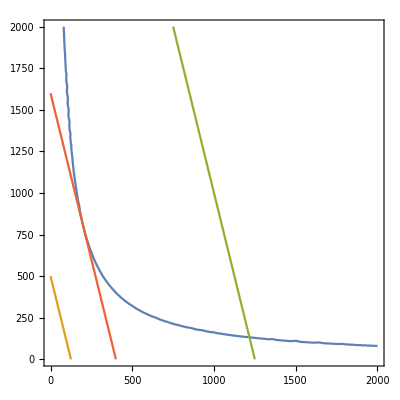

```mathematica
ContourPlot[{F[k,l]==20,c[k,l]==1000,c[k,l]==10000,c[k,l]==3200},{k,0,2000},{l,0,2000}]
```

```mathematica
Grad[F[k,l],{k,l}]
```

{l/(4 (k l)^(3/4)),k/(4 (k l)^(3/4))}

```mathematica
Grad[c[k,l],{k,l}]
```

{8,2}

```mathematica
Solve[{l/(4 (k l)^(3/4))==λ*8,k/(4 (k l)^(3/4))==λ*2,F[k,l]==20},{k,l,λ}]
```

{{k→-200,l→-800,λ→-1/320},{k→200,l→800,λ→1/320}}

```mathematica
{{k->-200,l->-800,λ->-1/320},{k->200,l->800,λ->1/320}}
```

```mathematica
c[200,800]
```

3200

## Example 3

```mathematica
f[x_,y_,z_]:=2*x-3*y+z
```

```mathematica
g[x_,y_,z_]:=x^2+y^2+z^2
```

```mathematica
ContourPlot3D[{g[x,y,z]==9,f[x,y,z]==0,f[x,y,z]==4,f[x,y,z]==11.225,f[x,y,z]==-11.225},{x,-4,4},{y,-4,4},{z,-4,4}]
```

-Graphics3D-

```mathematica
Grad[f[x,y,z],{x,y,z}]
Grad[g[x,y,z],{x,y,z}]
```

{2,-3,1}

{2 x,2 y,2 z}

```mathematica
NSolve[{λ*2*x==2,λ*2*y==(-3),λ*2*z==1,g[x,y,z]==9},{x,y,z,λ}]
```

{{x→1.60357,y→-2.40535,z→0.801784,λ→0.62361},{x→-1.60357,y→2.40535,z→-0.801784,λ→-0.62361}}

```mathematica
{{x->1.6035674514745464,y->-2.4053511772118195,z->0.8017837257372732,λ->1.6035674514745464},{x->-1.6035674514745468,y->2.4053511772118203,z->-0.8017837257372734,λ->-1.6035674514745468}}
```

```mathematica
f[x,y,z]/.{x->1.6035674514745464,y->-2.4053511772118195,z->0.8017837257372732,λ->1.6035674514745464}
```

11.225

```mathematica
f[x,y,z]/.{x->-1.6035674514745468,y->2.4053511772118203,z->-0.8017837257372734,λ->-1.6035674514745468}
```

-11.225

```mathematica
Grad[f[x,y,z]-λ*(g[x,y,z]-9),{x,y,z,λ}]==
```

```mathematica
{2-2 λ x,-3-2 λ y,1-2 λ z,9-x^2-y^2-z^2}
```

```mathematica
Exit[]
```

## Using the Lagrangian Approach

So far, we did not use the Lagrangian Method explictly. In the previous examples we just provided the geometric justification for the Lagrangian Method. Our learning goals are:

Given the objective function and the constraints, write the Lagrangian.

Write down in Mathematica the first-order conditions for the maximization  (gradient of the Lagrangian is zero).

Solve in Mathematica the system of equations in part 2 (the first-order conditions/gradient of the Lagrangian is zero).

Use your Economic reasoning to discard solutions that do not correspond to the maximum.

## An Example

Consider a consumer with preferences for clothing (c), food (f), and housing (h). The consumer faces two constraints: the standard budget constraint and another constraint the requires the combined expenditures  on food and housing to be match a percentage of the consumer’s income (80%).

Prices of these goods are respectively:

```mathematica
pc=1;
pf=10;
ph=6;
income = 100;
percentage = 0.8 (* 80% *)
```

0.8

```mathematica
u[c_,f_,h_]:=c*f*h^2 (* utility function *)
g1[c_,f_,h_]:={pc,pf,ph}.{c,f,h} (* expenditure on all goods  *)
g2[f_,h_]:={pf,ph}.{f,h} (* expenditures only on food and housing *)
ℒ[c_,f_,h_,λ1_,λ2_]:=u[c,f,h]-λ1*(g1[c,f,h]-income)-λ2*(g2[f,h]-percentage*income)
```

```mathematica
u[c,f,h]
g1[c,f,h]
g2[f,h]
```

c f h^2

c+10 f+6 h

10 f+6 h

Thus, the goal is to maximize u[c,f,h] subject to g1[c,f,h]=100 and g2[f,h] = 80.

```mathematica
gl=Grad[ℒ[c,f,h,λ1,λ2],{c,f,h,λ1,λ2}] (* Computing the Lagrangian *)
```

{f h^2-λ1,c h^2-10 λ1-10 λ2,2 c f h-6 λ1-6 λ2,100-c-10 f-6 h,80.-10 f-6 h}

Side-comment, the “Thread function”. You do not need to know this function but it help us to construct system of equations faster than typing equation by equation. See the examples

```mathematica
Thread[{a,b,c}=={x,w,z}]
Thread[{a,b,c}>7]
Thread[{a,b,c}==0]
```

{a==x,b==w,c==z}

{a>7,b>7,c>7}

{a==0,b==0,c==0}

#### Step 1.

```mathematica
eqs=Thread[gl==0] (* Gradient of the Lagrangian is set to zero *)
```

{f h^2-λ1==0,c h^2-10 λ1-10 λ2==0,2 c f h-6 λ1-6 λ2==0,100-c-10 f-6 h==0,80.-10 f-6 h==0}

```mathematica
Solve[eqs,{c,f,h,λ1,λ2}] (* Solving the gradient of the Lagrangian is zero for the variables*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c→20.,f→8.,h→0.,λ1→0.,λ2→0.},{c→20.,f→2.66667,h→8.88889,λ1→210.7,λ2→-52.6749}}

### A geometric view of the solution

Notice that with MORE THAN ONE CONSTRAINT the indifference surface of the objective curve will NOT be tangent to both indifference surfaces that correspond to the constraints. Instead, it will be tangent to the curve that corresponds to the intersection of both constraints. That curve is depicted in red below.

However, notice that the Lagrangian Method does still WORK but the geometric intuition is a difference than in the case of ONE constraint. The gradient of the objective function is not going to be proportional to the gradient of each constraint but it will equal to an weighted sum of the gradients of g1 and g2 (where the weights

```mathematica
p7:=ContourPlot3D[{g2[f,h]==80,g1[c,f,h]==100},{c,0,100},{f,0,10},{h,0,33.4}] (* both constraints *)
```

```mathematica
Solve[g1[c,f,h]==100 && g2[f,h]==80,{f,c}] (* region where both constraints are satisfied (intersect)*)
```

{{f→1/5 (40-3 h),c→20}}

```mathematica
p6:=ParametricPlot3D[{20,8-(3/5)*h,h},{h,0,33.4},PlotStyle->Red]  (* plot of region where both constraints are satisfied (intersect)*)
```

```mathematica
Show[p6,p7,AxesLabel->{"c","f","h"}]
```

-Graphics3D-

```mathematica
p8:=ContourPlot3D[{u[c,f,h]==4214
},{c,0,100},{f,0,10},{h,0,33.4}] (* indifference surface of the objective function evaluated at the optimal solution*)
```

```mathematica
Show[p8,p7]
```

-Graphics3D-

```mathematica
Show[p6,p8]
```

-Graphics3D-

## Using the Substitution Method instead of the Lagrangian

We use the two constraints to eliminate to variables and express the objective function as a function of a single variable.

```mathematica
u[c,f,h]/.Solve[g1[c,f,h]==100 && g2[f,h]==80,{f,c}]  (* value of the objective functin when both g1 and g2 are satisfied*)
```

4 (40-3 h) h^2

```mathematica
Solve[D[4 (40-3 h) h^2,h]==0]
```

{{h→0},{h→80/9}}

```mathematica
4.0 (40-3 h) h^2/.{h->80/9} (* We obtain the same value*)
```

4213.99

In general it may be difficult or impossible to explicitly solve for value of the variables in which all the constraints are satisfied so we will not use the substitution method in the future.